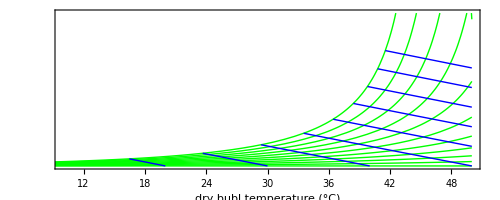

```mathematica
Module[{Psat,P,ϕω,Hω,p1,p2},
Psat[T_]=1000*10^(5.40221-1838.675/(T+241.263));
P=101.325;(*kPa*)

ϕω=Interpolation[Table[{T,Abs[0.622*((ϕ*Psat[T])/(P-ϕ*Psat[T]))]},{T,0,50,0.75}]];
Hω=Interpolation[Table[{T,100*(H-T)/(2500+2*T)},{T,0,50}]];

p1=Show[Table[{
Plot[ϕω[DBT],{DBT,0,50},PlotStyle->{Thick,Green},PlotRange->{{10,50},{0,3}}],
Graphics[]
},{ϕ,0,1,0.1}]];

p2=Show[Table[{
Plot[Piecewise[{{None,Evaluate[ϕω[DBT]/.ϕ->1]<Hω[DBT]},{Hω[DBT],Evaluate[ϕω[DBT]/.ϕ->1]≥Hω[DBT]}}],{DBT,0,50},PlotStyle->{Thick,Blue},PlotRange->{{10,50},{0,3}}],
Graphics[]
},{H,20,100,10}]];

Show[p1,p2,
Frame->True,
FrameLabel->{{None,Style[Column[{"specific humidity","(g moisture /kg dry air"},Center],17]},{Style["dry bubl temperature (°C)",17],None}},
FrameTicks->{{None,All},{All,None}},
LabelStyle->{Black,14},
AspectRatio->Full,
ImageSize->500]
]
```